# Specific Potential For Schrodinger Equation

## Animation

## Potential Distribution

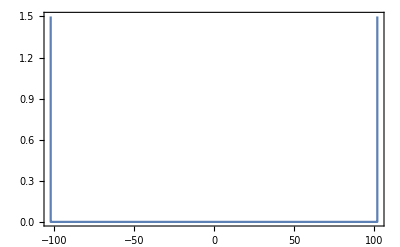

```mathematica
dt=0.01; Nsteps=50;T=120;
hbar=1; m=1.9; ntotal=2^11; 

dx=0.1; x`vec=Table[-1/2*ntotal*dx+i*dx,{i,0,ntotal-1}]; 
{index1,index2}={First@Flatten@Position[x`vec,First@Select[x`vec,-width<#<width&]],First@Flatten@Position[x`vec,Last@Select[x`vec,-width<#<width&]]};

V0=1.5; L=hbar/(√(2m V0)); width=3L;  Vx=Table[0,{i,Length[x`vec]}]; Vx[[-1]]=Vx[[1]]=10^6;  Vx[[index1;;index2]]=V0;

potential=Table[{x`vec[[i]],Vx[[i]]},{i,1,ntotal}];
ListLinePlot[potential,PlotRange->{Automatic,{0,V0}},Frame->True]
```

```mathematica
x0=-60*L; E0=0.2*V0; p0=√(2m*E0); k0=p0/hbar; v0=p0/m; a=hbar/(√(2*(2m E0/80)));
```

## Definition for wave functions

```mathematica
gauss`x[x_,a_,x0_,k0_]:=1/(√(a √π))ⅇ^(-1/2((x-x0)/a)^2+ⅈ x k0);
gauss`k[k_,a_,x0_,k0_]:=1/(√(a √π))ⅇ^(-1/2(a(k-k0))^2-ⅈ x0 (k-k0));
```

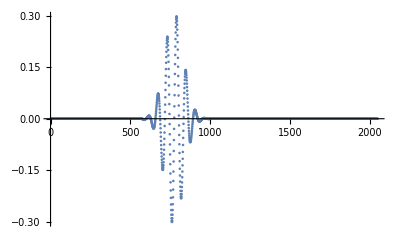

```mathematica
ListPlot[Re@gauss`x[a,x0,k0],PlotRange->All]
```

```mathematica
dk=(2π)/(ntotal*dx); k`vec=Table[-1/2 ntotal*dk+i*dk,{i,0,ntotal-1}];
```

```mathematica
psi`x0[x_]:=gauss`x[x,a,x0,k0];
psi`x[x_]:=psi`0[x];
psi`discrete`x[x_]:=dx/(√(2π))psi`x[x]*ⅇ^(-ⅈ k`vec[[0]] x);
psi`x[x_]:=psi`discrete`x[x]*ⅇ^(ⅈ k`vec[[0]] x)*(√(2π))/dx;
```

## Different Potential’s EigenStates

```mathematica
Schrodinger[{xmin_,xmax_},U_Function,NGrid_:101]:=Module[{dx=(xmax-xmin)/(NGrid-1),V`mat,T`mat,H`mat},
V`mat=DiagonalMatrix[U/@Range[xmin,xmax,dx]];
T`mat=DiagonalMatrix[Table[-1/(2(dx)^2)*(-2),NGrid]]+DiagonalMatrix[Table[-1/(2(dx)^2),NGrid-1],1]+DiagonalMatrix[Table[-1/(2(dx)^2),NGrid-1],-1];
H`mat=V`mat+T`mat;
Sort[Transpose[Eigensystem[N@H`mat]],#1[[1]]<#2[[1]]&]
];

Module[{},fun1=1/2#^2&;
fun2=Piecewise[{{1000,#<0},{1/2#^2,#>=0}}]&;
fun3=Piecewise[{{0,#<-1},{-20,-1≤#≤1},{0,#>1}}]&;
fun4=1/2#^2+2Exp[-2#^2]&;]

Manipulate[pot`fun=Switch[d,1,fun1,2,fun2,3,fun3,4,fun4];
sol=Schrodinger[{-10,10},pot`fun,1000];
eigenvalues=Transpose[sol][[1]];
eigenvecs=sol[[1;;-1,2]];
f1=ListLinePlot[Table[2.5eigenvecs[[i]]+eigenvalues[[i]],{i,levels}],PlotRange->{{-5,5},All},DataRange->{-10,10},Axes->False,Frame->True,PlotStyle->Dashed];
f2=ListLinePlot[Table[{x,pot`fun[x]},{x,-10,10,20/1000}],PlotRange->All];
Grid[{{Grid[Table[{Subscript["E", i],eigenvalues[[i]]},{i,levels}],Frame->All],Show[f1,f2,ImageSize->Medium]}}],
{{d,1,"Potential Type"},{1,2,3,4}},
{{levels,5,"Number of Levels"},Range[1,10,1],ControlType->SetterBar}]
```